```mathematica
Clear[p,kp,ki];

Jd=2*10^-3;
Jm=1;
b=4;
c=10^3;
i=50;
tau=3*10^-3;
s=0.05;
r=0.7;
k=100;

Jdpr=Jd*i^2;
spr=s*i^2;
rpr=r*i;

A={{Jdpr*p^2+b*p+c,-(b*p+c),-1,0},{-(b*p+c),Jm*p^2+b*p+c,0,0},{spr*p,0,tau*p+1,-rpr},{k*kp*p,k*ki,0,p}};

detA=Expand[Det[A]];

coeffs=CoefficientList[detA,p];

coeffsDescending=Reverse[coeffs];

detA==0
```

3.5×10^6 ki+14000. ki p+3.5×10^6 kp p+125000. p^2+14000. kp p^2+6500. p^3+3500. kp p^3+167. p^4+(634 p^5)/125+(3 p^6)/200==0

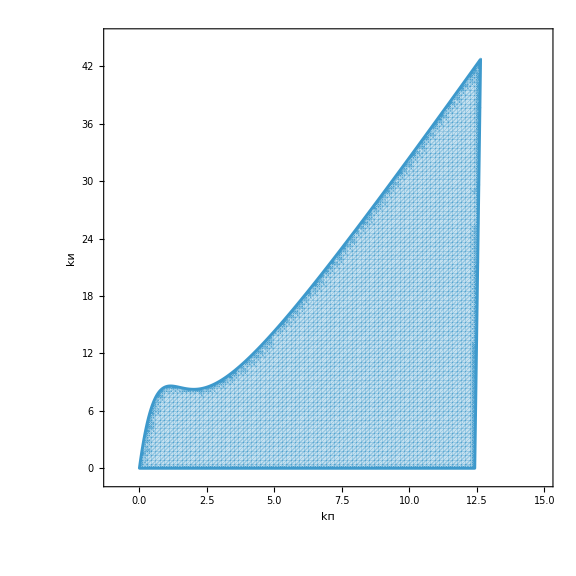

```mathematica
a=coeffsDescending;

H={{a[[2]],a[[4]],a[[6]],0,0,0},{a[[1]],a[[3]],a[[5]],a[[7]],0,0},{0,a[[2]],a[[4]],a[[6]],0,0},{0,a[[1]],a[[3]],a[[5]],a[[7]],0},{0,0,a[[2]],a[[4]],a[[6]],0},{0,0,a[[1]],a[[3]],a[[5]],a[[7]]}};

Delta1=Det[H[[1;;1,1;;1]]];
Delta2=Det[H[[1;;2,1;;2]]];
Delta3=Det[H[[1;;3,1;;3]]];
Delta4=Det[H[[1;;4,1;;4]]];
Delta5=Det[H[[1;;5,1;;5]]];
Delta6=Det[H[[1;;6,1;;6]]];

stab[kp_,ki_]:=UnitStep[Delta1]*UnitStep[Delta2]*UnitStep[Delta3]*UnitStep[Delta4]*UnitStep[Delta5]*UnitStep[Delta6];

RegionPlot[stab[kp,ki]==1,{kp,-1,15},{ki,-1,45},AxesLabel->{"kп","kи"},FrameLabel->{"kп","kи"},PlotPoints->100,MaxRecursion->4,ImageSize->Large, LabelStyle->Directive[Black,22],BaseStyle->{FontSize->18}]
```

```mathematica
NSolve[(detA/. {kp->10,ki->15})==0,p]
```

{{p→-329.53},{p→-2.54315-85.4706 ⅈ},{p→-2.54315+85.4706 ⅈ},{p→-1.50409},{p→-1.00628-31.0608 ⅈ},{p→-1.00628+31.0608 ⅈ}}

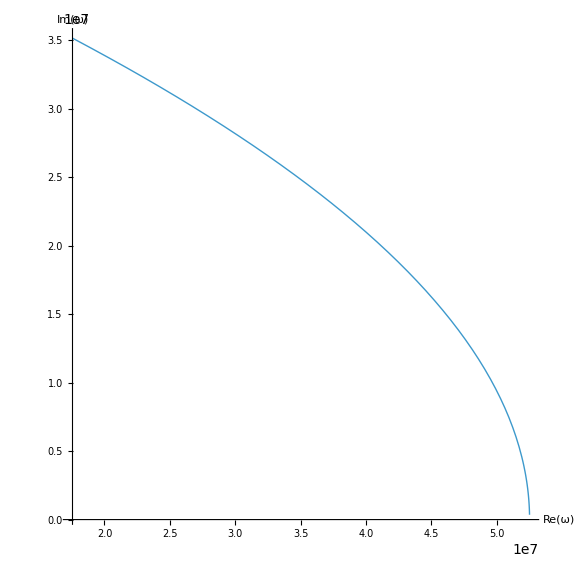

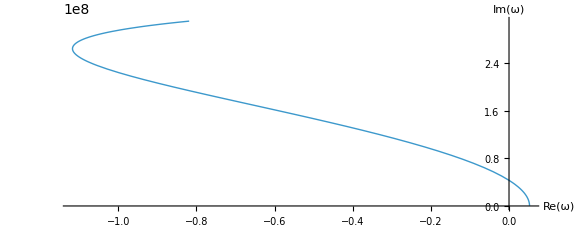

-Graphics-

```mathematica
kp=10;
ki=15;

ReW[w_]:=(3.5*10^6*ki-(14000*ki+3.5*10^6*kp)*w^2+(14000*kp+125000)*w^4-0.015*w^6);

ImW[w_]:=((3.5*10^6*kp+14000*ki)*w-(3500*kp+6500)*w^3+5.072*w^5);

mihailov1=ParametricPlot[{ReW[w],ImW[w]},{w,0.01,1},AxesLabel->{"Re(ω)","Im(ω)"},PlotRange->All,PlotStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];

mihailov10=ParametricPlot[{ReW[w],ImW[w]},{w,0.01,10},AxesLabel->{"Re(ω)","Im(ω)"},PlotRange->All,PlotStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];

mihailov5000=ParametricPlot[{ReW[w],ImW[w]},{w,0.01,5000},AxesLabel->{"Re(ω)","Im(ω)"},PlotRange->All,PlotStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];

mihailov1
mihailov10
mihailov5000
```

```mathematica
R[w_]:=Sqrt[ReW[w]^2+ImW[w]^2];

min=NMinimize[{R[w],w>0},w]

wMin=w/. min[[2]];
RMin=min[[1]];

stabilityMarginPlot=ParametricPlot[{ReW[w],ImW[w]},{w,0.01,10},AxesLabel->{"Re(ω)","Im(ω)"},PlotRange->{{-5*10^7,6*10^7},{-1*10^7,4*10^7}},PlotStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14},Epilog->{Red,PointSize[Large],Point[{ReW[wMin],ImW[wMin]}],Dashed,Line[{{0,0},{ReW[wMin],ImW[wMin]}}]}];

stabilityMarginPlot
```

{3.93058×10^7,{w→0.996626}}

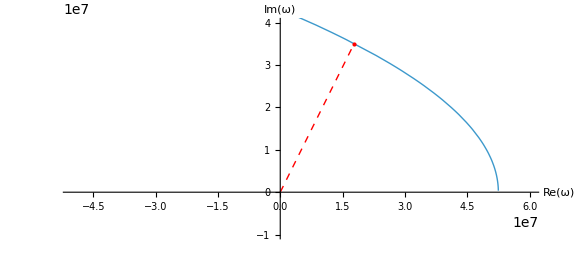

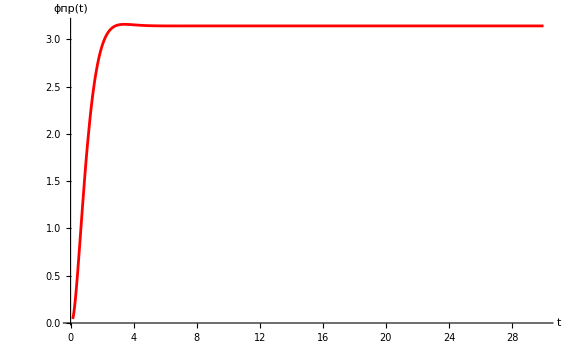

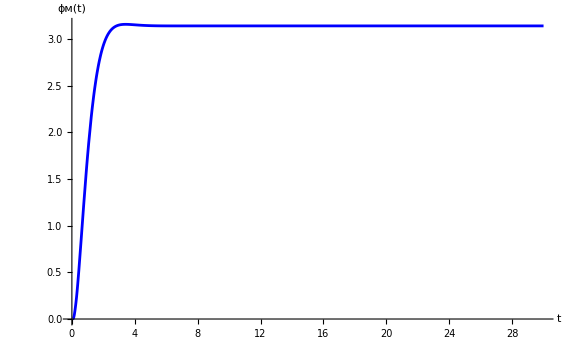

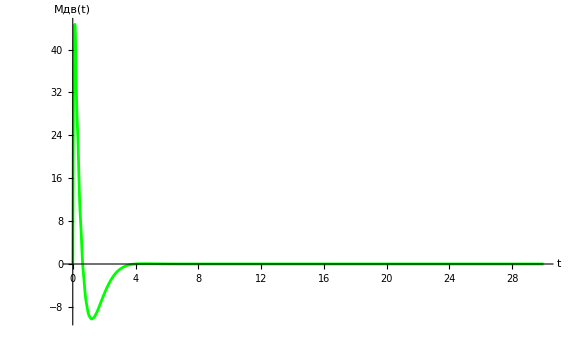

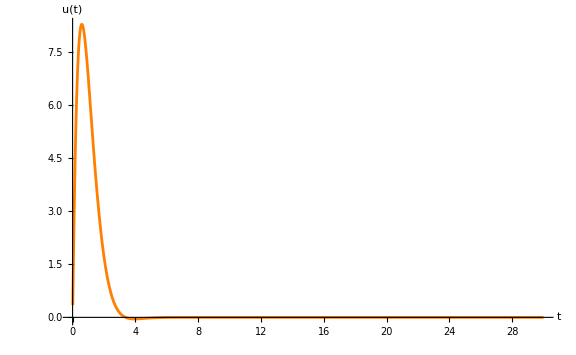

```mathematica
kp=0.1;
ki=0.1;

h={{0},{0},{0},{k*ki}};

X=Simplify[Inverse[A].h*Pi/p];

x=Flatten[InverseLaplaceTransform[X,p,t]];

g1=Plot[x[[1]],{t,0,30},PlotRange->All,PlotStyle->Red,AxesLabel->{"t","ϕпр(t)"},ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];

g2=Plot[x[[2]],{t,0,30},PlotRange->All,PlotStyle->Blue,AxesLabel->{"t","ϕм(t)"},ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];

g3=Plot[x[[3]],{t,0,30},PlotRange->All,PlotStyle->Green,AxesLabel->{"t","Mдв(t)"},ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];

g4=Plot[x[[4]],{t,0,30},PlotRange->All,PlotStyle->Orange,AxesLabel->{"t","u(t)"},ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];

g1
g2
g3
g4
```

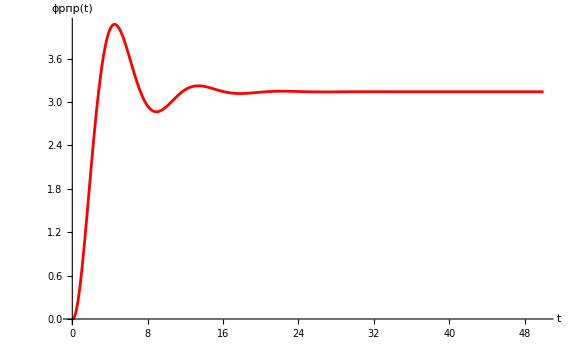
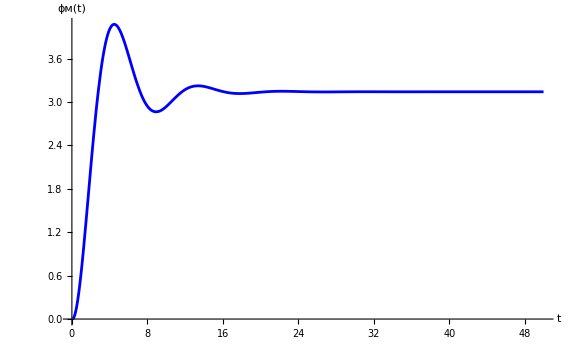
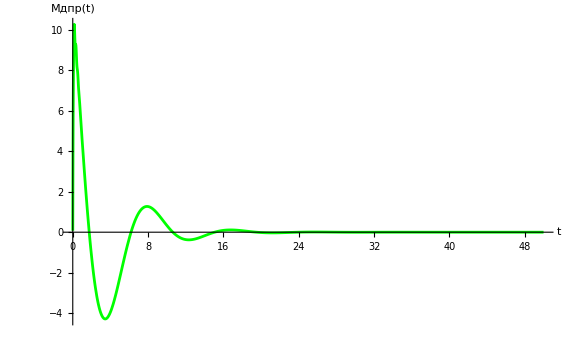
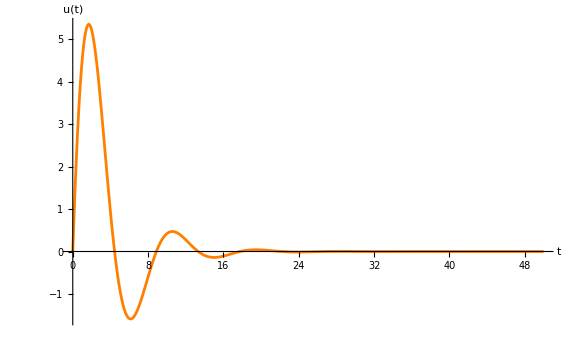

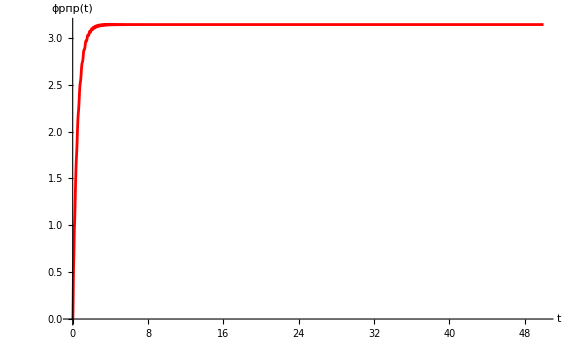
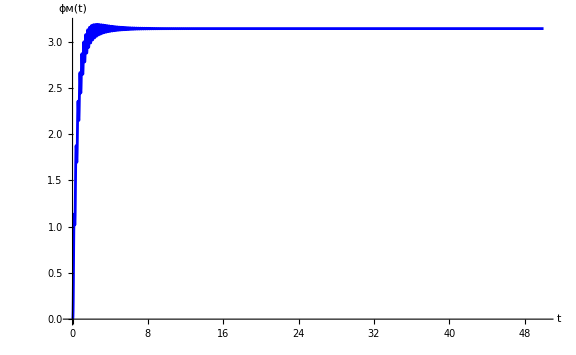
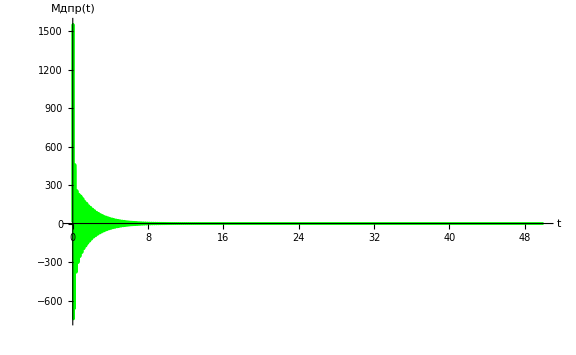
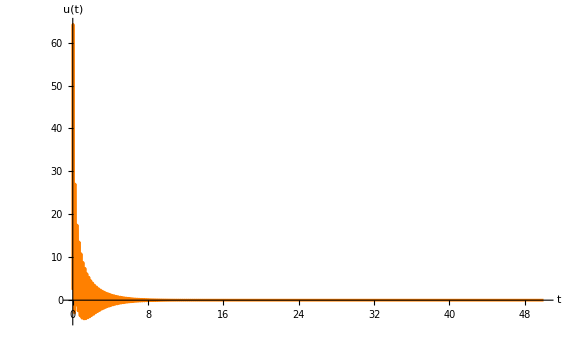

```mathematica
buildTransientPlots[kpValue_,kiValue_,name_]:=Module[{X,x,g1,g2,g3,g4},kp=kpValue;
ki=kiValue;
h={{0},{0},{0},{k*ki}};
X=Simplify[Inverse[A].h*Pi/p];
x=Flatten[InverseLaplaceTransform[X,p,t]];
g1=Plot[x[[1]],{t,0,50},PlotRange->All,PlotStyle->Red,AxesLabel->{"t","ϕрпр(t)"},ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];
g2=Plot[x[[2]],{t,0,50},PlotRange->All,PlotStyle->Blue,AxesLabel->{"t","ϕм(t)"},ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];
g3=Plot[x[[3]],{t,0,50},PlotRange->All,PlotStyle->Green,AxesLabel->{"t","Mдпр(t)"},ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];
g4=Plot[x[[4]],{t,0,50},PlotRange->All,PlotStyle->Orange,AxesLabel->{"t","u(t)"},ImageSize->Large,LabelStyle->Directive[Black,14],BaseStyle->{FontSize->14}];
Export["phi_pr_"<>name<>".pdf",g1];
Export["phi_m_"<>name<>".pdf",g2];
Export["Mdv_"<>name<>".pdf",g3];
Export["u_"<>name<>".pdf",g4];
{g1,g2,g3,g4}]

buildTransientPlots[0.02,0.02,"002_002"]
buildTransientPlots[5,10,"5_10"]
buildTransientPlots[10,25,"10_35"]
```

General::munfl: -7.0044×10^-10 3.45615×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.88562×10^-10 2.29068×10^-300 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.76842×10^-10 1.81698×10^-299 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.65312×10^-10 3.35546×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.53999×10^-10 3.5827×10^-300 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of `1` is too small to represent as a normalized machine number; precision may be lost. will be suppressed during this calculation.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

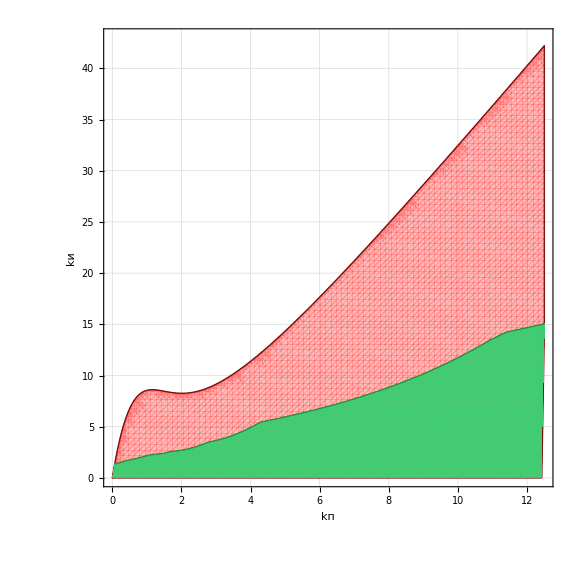

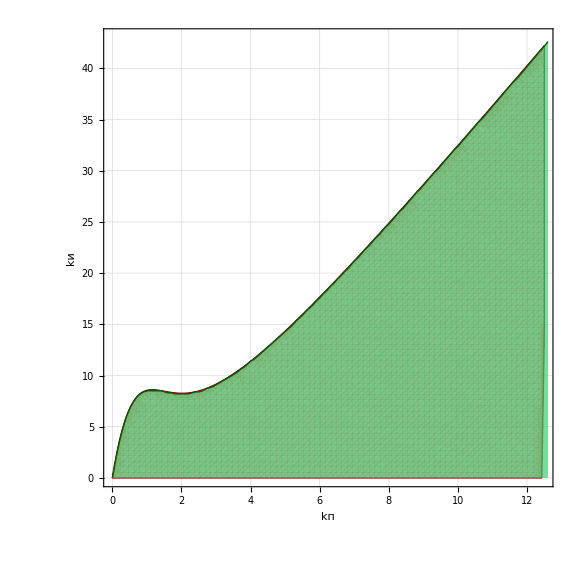

```mathematica
Clear[kp,ki,p,t,stab,maxMomentAtPointFast, maxSignalAtPointFast];

(*Область устойчивости по критерию Рауса--Гурвица*)
coeffs=coeffsDescending;
deltas={Delta1,Delta2,Delta3,Delta4,Delta5,Delta6};

stabilityIneq=And@@Thread[coeffs>0]&&And@@Thread[deltas>0];

stabilityRegion=RegionPlot[stabilityIneq,{kp,0,12.5},{ki,0,43},FrameLabel->{"kп","kи"},PlotPoints->100,MaxRecursion->4,ImageSize->Large,LabelStyle->Directive[Black,18],BaseStyle->{FontSize->16}];

(*Проверка принадлежности точки области устойчивости*)
stab[kpValue_?NumericQ,kiValue_?NumericQ]:=Module[{aValues,deltaValues},aValues=N[coeffs/. {kp->kpValue,ki->kiValue}];
deltaValues=N[deltas/. {kp->kpValue,ki->kiValue}];
And@@Thread[aValues>0]&&And@@Thread[deltaValues>0]];

(*Максимальный момент в одной точке области*)
maxMomentAtPointFast[kpValue_?NumericQ,kiValue_?NumericQ]:=Module[{Aloc,hloc,Xloc,xloc,MmExpr,values},Aloc=A/. {kp->kpValue,ki->kiValue};
hloc={{0},{0},{0},{k*kiValue}};
Xloc=Inverse[Aloc].hloc*Pi/p;
xloc=Flatten[InverseLaplaceTransform[Xloc,p,t]];
MmExpr=b*(D[xloc[[1]],t]-D[xloc[[2]],t])+c*(xloc[[1]]-xloc[[2]]);
values=Abs[N@Table[MmExpr/. t->tt,{tt,0,30,0.02}]];
Max[N[values]]];

maxSignalAtPointFast[kpValue_?NumericQ,kiValue_?NumericQ]:=Module[{Aloc,hloc,Xloc,xloc,uExpr,values},Aloc=A/. {kp->kpValue,ki->kiValue};
hloc={{0},{0},{0},{k*kiValue}};
Xloc=Inverse[Aloc].hloc*Pi/p;
xloc=Flatten[InverseLaplaceTransform[Xloc,p,t]];
uExpr=xloc[[4]];
values=Abs[Table[uExpr/. t->tt,{tt,0,30,0.02}]];
Max[N[values]]]

(*Покрываем устойчивую область сеткой*)
kpValues=Union[Range[0.01,15,0.5],{12.4}];
kiValues=Union[Range[0.01,45,1],{45}];

dataLimits=Flatten[ParallelTable[If[stab[kp0,ki0],{kp0,ki0,maxMomentAtPointFast[kp0,ki0], maxSignalAtPointFast[kp0,ki0]},Nothing],{kp0,kpValues},{ki0,kiValues}],1];
(*Точки,удовлетворяющие ограничению по моменту*)
dataMomentClipped=Select[dataLimits,#[[3]]<=150&];

(* =====Область устойчивости=====*)stabilityRegion=RegionPlot[stabilityIneq,{kp,0,12.5},{ki,0,43},PlotStyle->Directive[RGBColor[1,0.4,0.4],Opacity[0.45]],BoundaryStyle->Directive[DarkRed,Thick],PlotPoints->80,MaxRecursion->3];



(* =====Допустимая область по моменту=====*)

momentAllowedRegion=ListContourPlot[dataLimits[[All,{1,2,3}]],Contours->{150},ContourShading->{Directive[RGBColor[0.25,0.8,0.45],Opacity[0.7]],None},ContourStyle->Directive[DarkGreen,Thick],InterpolationOrder->1];



(* =====Совмещённый график=====*)

Show[stabilityRegion,momentAllowedRegion,Frame->True,FrameLabel->{"kп","kи"},PlotRange->{{0,12.5},{0,43}},ImageSize->Large,LabelStyle->Directive[Black,18],BaseStyle->{FontSize->16},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85]],PlotLegends->Placed[{Style["область устойчивости",DarkRed],Style["допустимый момент",DarkGreen]},{0.8,0.82}]]

signalBoundary=Table[Module[{points},points=Select[dataLimits,#[[1]]==kp0&&#[[4]]<=220&];
If[points==={},Nothing,{kp0,Max[points[[All,2]]]}]],{kp0,kpValues}];

signalAllowedRegion=ListLinePlot[signalBoundary,Filling->Bottom,PlotStyle->Directive[DarkGreen,Thick],FillingStyle->Directive[RGBColor[0.25,0.8,0.45],Opacity[0.7]],InterpolationOrder->1];

Show[stabilityRegion,signalAllowedRegion,Frame->True,FrameLabel->{"kп","kи"},PlotRange->{{0,12.5},{0,43}},ImageSize->Large,LabelStyle->Directive[Black,18],BaseStyle->{FontSize->16},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85]],PlotLegends->Placed[{Style["область устойчивости",DarkRed],Style["допустимый сигнал",DarkGreen]},{0.8,0.82}]]
```

```mathematica
(*Итоговая допустимая область:устойчивость+момент+сигнал*)allowedBoth=Select[dataLimits,#[[3]]<=150&&#[[4]]<=220&];

MaximalBy[allowedBoth,#[[3]]&][[1]]

MaximalBy[allowedBoth,#[[4]]&][[1]]
```

{4.51,5.61,149.989,36.5706}

{12.21,14.81,149.765,62.5976}

```mathematica
Clear[settlingTimeAtPointFast];

settlingTimeAtPointFast[kpValue_?NumericQ,kiValue_?NumericQ]:=Module[{Aloc,hloc,Xloc,xloc,phiMExpr,timeGrid,vals,outside},Aloc=A/. {kp->kpValue,ki->kiValue};
hloc={{0},{0},{0},{k*kiValue}};
Xloc=Inverse[Aloc].hloc*Pi/p;
xloc=Flatten[InverseLaplaceTransform[Xloc,p,t]];
phiMExpr=xloc[[2]];
timeGrid=Range[0,40,0.01];
vals=N[phiMExpr/. t->#]&/@timeGrid;
outside=Pick[timeGrid,Abs[vals-Pi]>0.1*Pi];
If[outside==={},0,Min[40,Last[outside]+0.01]]]

Clear[dataSettling];

dataSettling=ParallelMap[{#[[1]],#[[2]],settlingTimeAtPointFast[#[[1]],#[[2]]]}&,allowedBoth];

tpRegionPlot=ListDensityPlot[dataSettling,InterpolationOrder->1,ColorFunction->"Rainbow",Frame->True,FrameLabel->{"kп","kи"},PlotLegends->Placed[BarLegend[{"Rainbow",MinMax[dataSettling[[All,3]]]},LegendLabel->"tп, c"],Right],ImageSize->Large,LabelStyle->Directive[Black,18],BaseStyle->{FontSize->16},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85]]];

tpRegionPlot

tpContourPlot=ListContourPlot[dataSettling,InterpolationOrder->1,Contours->10,ContourLabels->True,ColorFunction->"Rainbow",Frame->True,FrameLabel->{"kп","kи"},PlotLegends->Placed[BarLegend[{"Rainbow",MinMax[dataSettling[[All,3]]]},LegendLabel->"tп, c"],Right],ImageSize->Large,LabelStyle->Directive[Black,18],BaseStyle->{FontSize->16},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.85]]];

tpContourPlot
```

General::munfl: -7.0044×10^-10 7.38019×10^-300 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.88562×10^-10 2.29059×10^-300 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -7.0044×10^-10 3.45615×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.88562×10^-10 1.05261×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.80172×10^-10 2.62358×10^-300 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of `1` is too small to represent as a normalized machine number; precision may be lost. will be suppressed during this calculation.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Pick::incomp: Expressions {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,«6»,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«3951»} and {3.14159,3.14159,3.14159,3.14159,3.14158,3.14154,3.14148,3.14138,«35»,3.07903,3.0758,3.0725,3.06912,3.06566,3.06212,3.0585,«3951»}>«19» have incompatible shapes.

Pick::incomp: Expressions {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,«6»,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«3951»} and {3.14159,3.14159,3.14154,3.14124,3.14023,3.13781,3.13304,3.12488,«35»,1.97852,1.95564,1.93302,1.91055,1.88814,1.8657,1.84318,«3951»}>«19» have incompatible shapes.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

Pick::incomp: Expressions {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,«6»,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«3951»} and {3.14159,3.14159,3.14159,3.14154,3.14141,3.14107,3.1404,3.13922,«35»,2.46688,2.43305,2.39855,2.36338,2.32751,2.29092,2.25361,«3951»}>«19» have incompatible shapes.

Pick::incomp: Expressions {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,«6»,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«3951»} and {3.14159,3.14159,3.14154,3.1412,3.14007,3.13734,3.13199,3.12282,«35»,1.86098,1.83669,1.8127,1.78888,1.76514,1.74139,1.71757,«3951»}>«19» have incompatible shapes.

Pick::incomp: Expressions {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,«6»,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«3951»} and {3.14159,3.14159,3.14152,3.14111,3.13975,3.13648,3.13013,3.11939,«35»,2.12985,2.10711,2.08612,2.06673,2.04876,2.03195,2.01605,«3951»}>«19» have incompatible shapes.

General::stop: Further output of Expressions `1` and `2` have incompatible shapes. will be suppressed during this calculation.

$Aborted

tpRegionPlot